```mathematica
dPhi=941;Tm=110;
vb[kappa_]:=√(dPhi/(Tm(1-3/(2 kappa))))
vbAlt=√(dPhi/Tm);
```

#### Limiting expression from journal__20180125__limiting expression_kappa_Barbosa__cylindrical_soln.nb

```mathematica
kapBarbLim[w_,vb_,kappa_]:=((kappa^(1/2)Gamma[kappa-1/2])/(2 Gamma[kappa])+vb/(√π w)Hypergeometric2F1[1/2,kappa,3/2,-vb^2/(kappa w^2)])^-1(((kappa+((-1+2 kappa) vb^2)/w^2) Gamma[-1/2+kappa])/(2 √kappa Gamma[kappa])+(2 vb^3 Hypergeometric2F1[1/2,1+kappa,3/2,-vb^2/(kappa w^2)])/(√π w^3)-((1+vb^2/(kappa w^2))^-kappa ((1+2 kappa) vb^2+2 kappa^2 w^2-2 kappa^2 w^2 Hypergeometric2F1[1,-1/2-kappa,1/2,-vb^2/(kappa w^2)]))/((-1+4 kappa^2) √π vb w))
```

```mathematica
barbAsymp[deltaPhi_,T_]:=1+2(√(deltaPhi/T))/Erfc[-√(deltaPhi/T)] NIntegrate[Erfc[x],{x,-√(deltaPhi/T),∞}]
```

#### The cylindrical-coord version of the Barbosa func, in terms of bulk velocity v_(b,th) = v_b/v_th=√(ΔΦ/(k T)) normalized by the thermal velocity v_th= √(kT/m)(origin: journal__20180125__somesing_work)

```mathematica
vbth[deltaPhi_,T_]:=√(deltaPhi/T);
```

```mathematica
normFacAlt[vbth_,kappa_]:=2/(π^(1/2)(kappa - 3/2)^(3/2))(1/2 Gamma[kappa-1/2]/Gamma[kappa+1]+vbth/(√π kappa(kappa-3/2)^(1/2))Hypergeometric2F1[1/2,kappa,3/2,-vbth^2/(kappa-3/2)])^-1;
funcAlt[rho_,phi_,vbth_,kappa_,b_]:=(1+(rho^2+vbth^2-2 vbth rho (1 - (Sin[phi])^2 b)^(1/2))/(kappa-3/2 ))^(-(kappa+1))
```

Old version, incorrect norm ...

```mathematica
(*normFacAlt[vbNormW_,kappa_]:=2/(π^(1/2)(2 kappa - 3)^(3/2))(1/2(kappa^(3/2)Gamma[kappa-1/2])/Gamma[kappa+1]+vbNormW/(√π)Hypergeometric2F1[1/2,kappa,3/2,-vbNormW^2/kappa])^-1
funcAlt[rho_,phi_,vb_,kappa_,b_]:=(1+(rho^2+vb^2-2 vb rho (1 - (Sin[phi])^2 b)^(1/2))/(2kappa-3 ))^(-(kappa+1))*)
```

## Now for some plots!

```mathematica
kaps=1.6;ParametricPlot3D[{rho Cos[phi],rho Sin[phi],Log[10,normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,0.1]]},{rho,0,6},{phi,-π/2,π/2},PlotRange->All,PlotPoints->80]
```

-Graphics3D-

```mathematica
kaps=1.6;ParametricPlot3D[{rho Cos[phi],rho Sin[phi],normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,1]},{rho,0,6},{phi,-π/2,π/2},PlotRange->All,PlotPoints->80]
```

-Graphics3D-

```mathematica
kaps=5;ParametricPlot3D[{rho Cos[phi],rho Sin[phi],normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,1]},{rho,0,6},{phi,-π/2,π/2},PlotRange->All,PlotPoints->80]
```

-Graphics3D-

```mathematica
kaps=5;ParametricPlot3D[{rho Cos[phi],rho Sin[phi],normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,0]},{rho,0,6},{phi,-π/2,π/2},PlotRange->All,PlotPoints->80]
```

-Graphics3D-

```mathematica
kaps=1.6;ParametricPlot3D[{rho Cos[phi],rho Sin[phi],Log[10,normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,1/72]]},{rho,0,6},{phi,-π/2,π/2},PlotRange->{{0,6},{-6,6},{-3,2}},PlotPoints->100,ImageSize->900]
```

-Graphics3D-

```mathematica
colors={Black,Gray,Orange,Red,Brown,Green,Purple};
kappas = {1.6,1.7,2,2.45,4,100};
```

```mathematica
placeList={Above,Above,Above,Above,Above,Above,Above};
nDigs={3,3,2,3,2,2,2,2};
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,6}];
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,6}];
```

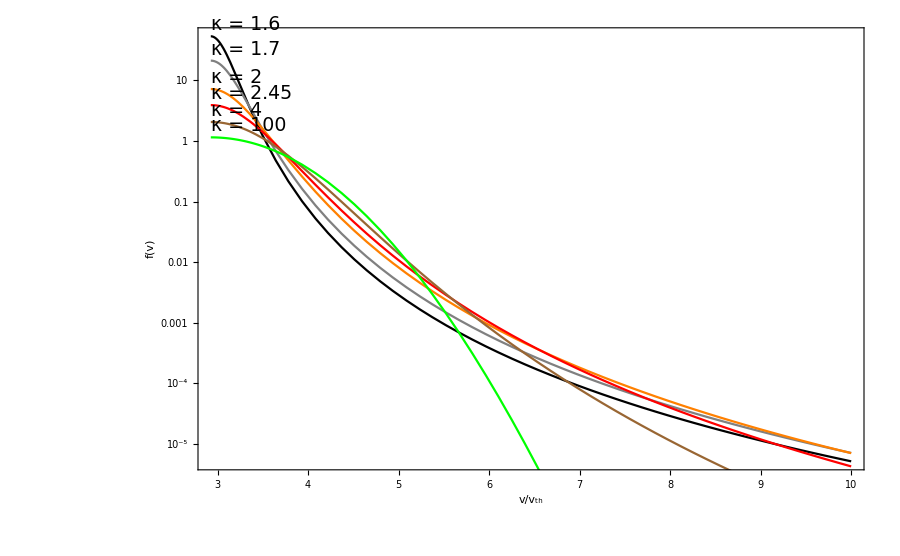

```mathematica
Show[Table[LogPlot[normFacAlt[vbth[dPhi,Tm],kappas[[k]]]funcAlt[rho,0,vbth[dPhi,Tm],kappas[[k]],0],{rho,vbth[dPhi,Tm],10},PlotStyle->colors[[k]],Frame->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],LabelStyle->(FontSize->19),FrameLabel->{StringForm["v/v_th"],StringForm["f(v)"]},ImageSize->900],{k,{1,2,3,4,5,6}}]]
```

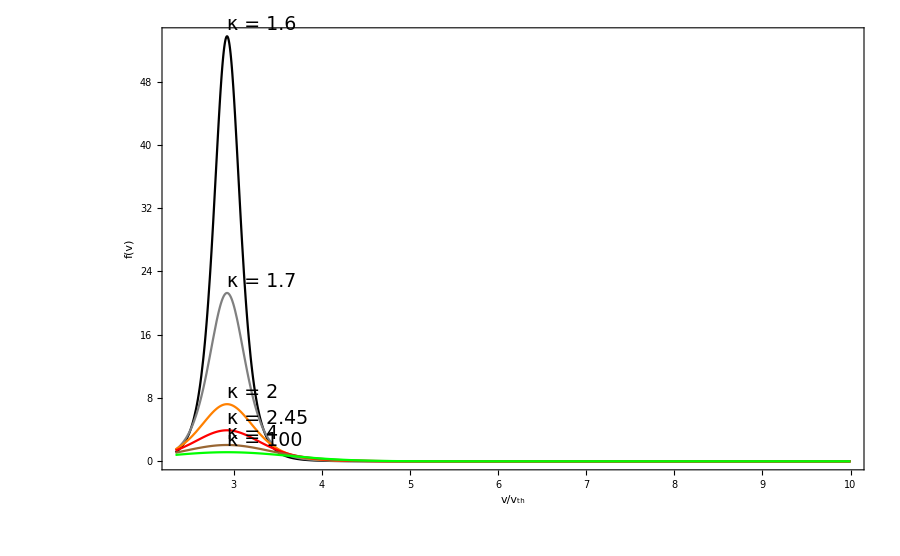

```mathematica
Show[Table[Plot[normFacAlt[vbth[dPhi,Tm],kappas[[k]]]funcAlt[rho,0,vbth[dPhi,Tm],kappas[[k]],0],{rho,vbth[dPhi,Tm]*4/5,10},PlotStyle->colors[[k]],PlotRange->All,Frame->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],LabelStyle->(FontSize->19),FrameLabel->{StringForm["v/v_th"],StringForm["f(v)"]},ImageSize->900],{k,{1,2,3,4,5,6}}]]
```

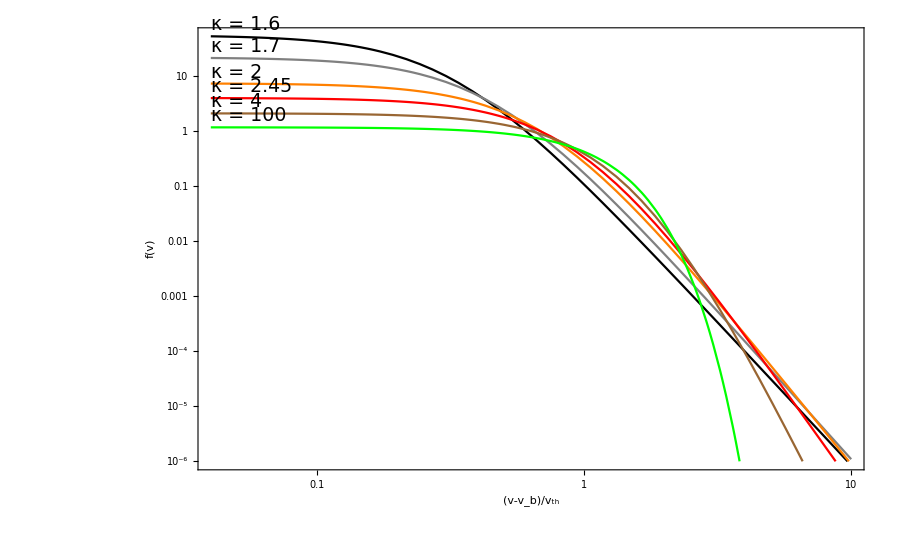

```mathematica
Show[Table[LogLogPlot[normFacAlt[vbth[dPhi,Tm],kappas[[k]]]funcAlt[rho+vbth[dPhi,Tm],0,vbth[dPhi,Tm],kappas[[k]],0],{rho,0.04,10},PlotStyle->colors[[k]],PlotRange->{{0.05,10},{1*^2,1*^-6}},Frame->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],LabelStyle->(FontSize->19),FrameLabel->{StringForm["(v-v_b)/v_th"],StringForm["f(v)"]},ImageSize->900],{k,{1,2,3,4,5,6}}]]
```

## Plot using old version

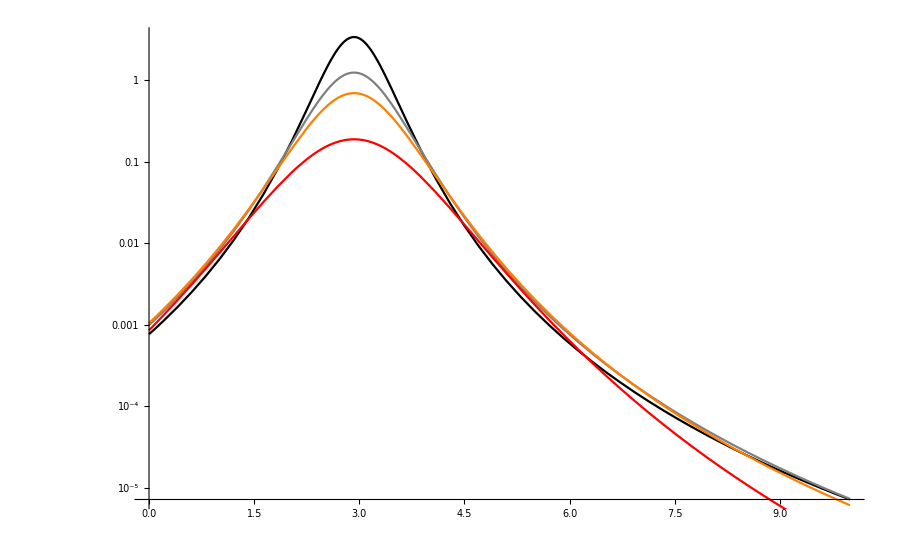

```mathematica
Show[Table[LogPlot[normFacAlt[vb[kappas[[k]]],kappas[[k]]]funcAlt[rho,0,vbAlt,kappas[[k]],0],{rho,0,10},PlotStyle->colors[[k]],ImageSize->900],{k,{1,2,3,4}}]]
```